# Schwarzschild geodesics

## Lagrangian and equations of motion

```mathematica
ClearAll[Lagrangian];

Lagrangian=1/2(-(f[x[λ],y[λ],z[λ]]/g[x[λ],y[λ],z[λ]])^2 t'[λ]^2+g[x[λ],y[λ],z[λ]]^4(x'[λ]^2+y'[λ]^2+z'[λ]^2));

ClearAll[tDot];
tDot=Solve[En==-D[Lagrangian,t'[λ]],t'[λ]]⟦1⟧;

ClearAll[EulerLagrangeFory,EulerLagrangeForz];
EulerLagrangeForx=Collect[(D[D[Lagrangian,x'[λ]],λ]-D[Lagrangian,x[λ]]==0)//.tDot,{x[λ],x'[λ],x''[λ]},FullSimplify];
EulerLagrangeFory=Collect[(D[D[Lagrangian,y'[λ]],λ]-D[Lagrangian,y[λ]]==0)//.tDot,{x[λ],x'[λ],x''[λ]},FullSimplify];
EulerLagrangeForz=Collect[(D[D[Lagrangian,z'[λ]],λ]-D[Lagrangian,z[λ]]==0)//.tDot,{x[λ],x'[λ],x''[λ]},FullSimplify];

ClearAll[normalization]
normalization=FullSimplify[Solve[(Lagrangian==δ/2)//.tDot,En,Reals]];
```

## Solution

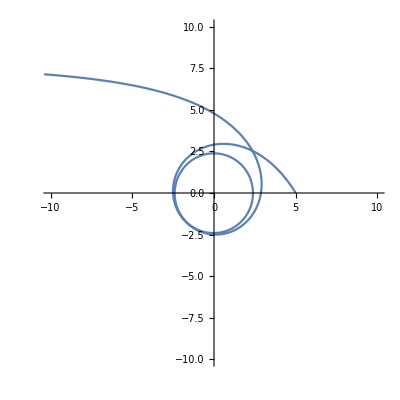

Mass: 1

Particle: Photon

Local positions: {5,0,0}

Local Veolocities: {-0.307303,0.490476,0.}

```mathematica
ClearAll[r,f,g];
r[x_,y_,z_]:=√(x^2+y^2+z^2);
f[x_,y_,z_]:=1-(2M)/(4r[x,y,z]);
g[x_,y_,z_]:=1+(2M)/(4r[x,y,z]);

ClearAll[M,δ];
M=1;
δ=0;

ClearAll[x0,y0,z0];
x0=5;
y0=0;
z0=0;

(* Local velocity *)
ClearAll[Vx0,Vy0,Vz0,normV];
Vx0=-62654*10^-5;
Vy0=1;
Vz0=0;

normV=(g[x0,y0,z0]^4 Vx0^2+g[x0,y0,z0]^4 Vy0^2+g[x0,y0,z0]^4 Vz0^2);

If[δ==0,
Vx0/=normV;
Vy0/=normV;
Vz0/=normV;
];

(* Global energy *)
ClearAll[En];
En=1;

ClearAll[λ0,λf];
λ0=0;
λf=100;

ClearAll[wp,ag,pg];
wp=20;
ag=wp-5;
pg=ag;

ClearAll[sol];
sol=NDSolve[
{
t'[λ]==(t'[λ]/.tDot),
EulerLagrangeForx,
EulerLagrangeFory,
EulerLagrangeForz,

(* global = local/lapse *)
x'[λ0]==Vx0*(f[x0,y0,z0]/g[x0,y0,z0])^-1,
y'[λ0]==Vy0*(f[x0,y0,z0]/g[x0,y0,z0])^-1,
z'[λ0]==Vz0*(f[x0,y0,z0]/g[x0,y0,z0])^-1,

t[0]==0,
x[λ0]==x0,
y[λ0]==y0,
z[λ0]==z0
},
{t,x,y,z},
{λ,λ0,λf},
WorkingPrecision->wp,
AccuracyGoal->ag,
PrecisionGoal->pg
]⟦1⟧;

ClearAll[range];
range=10;
ParametricPlot[{x[λ]//.sol,y[λ]//.sol},{λ,λ0,λf},PlotRange->{{-range,range},{-range,range}}]


Print["Mass: ",M];
Print["Particle: ",If[δ==0,"Photon","Massive"]]
Print["Local positions: {",x0,",",y0,",",z0,"}"]; 
Print["Local Veolocities: {",Vx0//N,",",Vy0//N,",",Vz0//N,"}"]; 

ClearAll[r,f,g];
ClearAll[M,δ];
ClearAll[x0,y0,z0];
ClearAll[Vx0,Vy0,Vz0];
ClearAll[En];
```